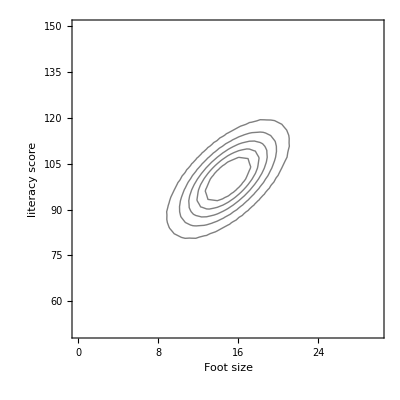

```mathematica
aMultiNormalPDF[x_,y_]:=PDF[MultinormalDistribution[{15,100},{{10,20},{20,100}}],{x,y}]
a1=Show[Plot3D[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},PlotRange->Full,ViewPoint->{-1.0247702550719293,-2.1545047299507063,2.399573981551678},ViewVertical->{0.,0.,1.},BaseStyle->{FontSize->16},AxesLabel->{"Foot size","literacy score","pdf"},Ticks->{True,True,None},ColorFunction->"PigeonTones"],ImageSize->Large];
a2=ContourPlot[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},Contours->{0.001,0.002,0.003,0.004,0.005},PlotRange->Full,Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{"Foot size","literacy score"},BaseStyle->{FontSize->16}];
Show[GraphicsRow[{a1,a2}],ImageSize->Large]
```

```mathematica
aMarginalIQ[IQ_] = Integrate[aMultiNormalPDF[FS,IQ],{FS,0,30}];
aMarginalFS[FS_] = Integrate[aMultiNormalPDF[FS,IQ],{IQ,50,150}];
gIQ=Rotate[Plot[aMarginalIQ[IQ],{IQ,50,150},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{IQ,"p(IQ)"}],Pi/2];
gFS=Show[Plot[aMarginalFS[FS],{FS,0,30},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{Foot size,"p(FS)"}],ImagePadding->{{30,30},{30,30}}];
Show[GraphicsGrid[{{a2,gIQ},{gFS,}}],ImageSize->Large]
```

-Graphics-

```mathematica
Clear[pIQConditionalOnFS,pConditional1]
```

```mathematica
FS1 = 10;
FS2 = 20;
aAnnotated1=ContourPlot[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},Contours->{0.001,0.002,0.003,0.004,0.005},PlotRange->Full,Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{"Foot size","literacy \n score"},BaseStyle->{FontSize->16},Epilog->{Blue,Dashed,Line[{{FS1,0},{FS1,150}}]}];
aAnnotated2=ContourPlot[aMultiNormalPDF[x,y],{x,0,30},{y,50,150},Contours->{0.001,0.002,0.003,0.004,0.005},PlotRange->Full,Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{"Foot size","literacy \n score"},BaseStyle->{FontSize->16},Epilog->{Blue,Dashed,Line[{{FS2,0},{FS2,150}}]}];
pIQConditionalOnFS[FS_,IQ_]:=aMultiNormalPDF[FS,IQ]/aMarginalFS[FS];
pConditional1[IQ_] := pIQConditionalOnFS[FS1,IQ];
pConditional2[IQ_] := pIQConditionalOnFS[FS2,IQ];
gConditional1=Rotate[Plot[pConditional1[IQ],{IQ,50,150},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{"score","p(score)"}],Pi/2];
gConditional2 = Rotate[Plot[pConditional2[IQ],{IQ,50,150},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{"score","p(score)"}],Pi/2];
gFinal=Show[GraphicsGrid[{{aAnnotated1,gConditional1},{aAnnotated2,gConditional2}}],ImageSize->600]
```

-Graphics-

```mathematica
Export["Probability_footSizeIntelligenceConditional.pdf",gFinal]
```

Probability_footSizeIntelligenceConditional.pdf